Más información sobre los patrones

Existe todo un sublenguaje de patrones en Wolfram Language. Hasta ahora se han visto ya algunos de sus elementos más importantes.

_ (“guion-bajo”) representa cualquier cosa. x_ (“x guion-bajo”) representa cualquier cosa, pero la denomina x. _h representa cualquier cosa que tenga encabezado h. Y, por último, x_h representa cualquier cosa que tenga encabezado h, y le da el nombre x.

Defina una función cuyo argumento sea un entero llamado n:

```mathematica
digitback[n_Integer]:=Framed[Reverse[IntegerDigits[n]]]
```

La función se evalúa cuando el argumento es entero:

```mathematica
{digitback[1234],digitback[6712],digitback[x],digitback[{4,3,2}],digitback[2^32]}
```

{{4,3,2,1},{2,1,7,6},digitback[x],digitback[{4,3,2}],{6,9,2,7,6,9,4,9,2,4}}

En ocasiones, se desea imponer alguna condición a un patrón. Para esto, se usa /; (“diagonal punto y coma”). n_Integer/;n>0 quiere decir cualquier entero mayor que 0.

De una definición que se aplique solo cuando n>0:

```mathematica
pdigitback[n_Integer/;n>0]:=Framed[Reverse[IntegerDigits[n]]]
```

La definición dada no se aplica a números negativos:

```mathematica
{pdigitback[1234],pdigitback[-1234],pdigitback[x],pdigitback[2^40]}
```

{{4,3,2,1},pdigitback[-1234],pdigitback[x],{6,7,7,7,2,6,1,1,5,9,9,0,1}}

El /; puede ponerse donde sea, incluso al final de toda la definición.

Defina diferentes casos para la función check:

```mathematica
check[x_,y_]:=Red/;x>y
```

```mathematica
check[x_,y_]:=Green/;x≤y
```

He aquí algunos ejemplos de la función check:

```mathematica
{check[1,2],check[2,1],check[3,4],check[50,60],check[60,50]}
```

{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}

__ (“doble guion-bajo”) representa cualquier secuencia de uno o más argumentos. ___ (“triple guion-bajo”) representa cero o más.

Defina una función que busque negro y blanco (en ese orden) en una lista.

El patrón coincide con negro seguido de blanco, con cualquier elemento anterior a, entre, o después de ellos:

```mathematica
blackwhite[{___,Black,m___,White,___}]:={1,m,2,m,3,m,4}
```

Elija la secuencia (la más corta) entre un negro y un blanco:

```mathematica
blackwhite[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],4}

Por defecto, __ y ___ eligen las coincidencias más cortas que funcionen. Puede usarse  Longest para que elijan, en vez de eso, las más largas.

Especifique que la secuencia entre negro y blanco sea lo más larga posible:

```mathematica
blackwhitex[{___,Black,Longest[m___],White,___}]:={1,m,2,m,3,m,4}
```

Ahora, m elige todos los elementos hasta el último blanco:

```mathematica
blackwhitex[{RGBColor[1, 0.5, 0.5],GrayLevel[0],RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],GrayLevel[1]}]
```

{1,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],2,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],3,RGBColor[1, 0.5, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],RGBColor[0.5, 0, 0.5],4}

x|y|z indica las coincidencias con x, y o z. x.. coincide con cualquier número de repeticiones de x.

bwcut corta, en efecto, la secuencia más larga que contenga solo negro y blanco:

```mathematica
bwcut[{a___,Longest[(Black|White)..],b___}]:={{a},Red,{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},RGBColor[1, 0, 0],{RGBColor[1, 1, 0]}}

El patrón x_ es, de hecho, la abreviatura de x:_, que significa “coincide con cualquier cosa (o sea, _) y al resultado le llama x”. También se puede usar la notación del tipo x: para patrones más complicados.

Forme un patrón denominado m que coincida con una lista de dos parejas:

```mathematica
grid22[m:{{_,_},{_,_}}]:=Grid[m,Frame->All]
```

```mathematica
{grid22[{{a,b},{c,d}}],grid22[{{12,34},{56,78}}],grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}
```

{a | b
c | d,12 | 34
56 | 78,grid22[{123,456}],grid22[{{1,2,3},{4,5,6}}]}

Denomine a la secuencia de negro y blanco, de modo que pueda usarse en el resultado:

```mathematica
bwcut[{a___,r:Longest[(Black|White)..],b___}]:={{a},Framed[Length[{r}]],{b}}
```

```mathematica
bwcut[{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],GrayLevel[0],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0]}]
```

{{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]},5,{RGBColor[1, 1, 0]}}

Como último ejemplo, se usarán patrones para implementar el algoritmo clásico de ciencias de la computación para ordenar una lista, que intercambia repetidamente parejas de elementos sucesivos que estén fuera de orden. No es difícil escribir cada paso del algoritmo como una sustitución para el patrón.

Sustituya los primeros elementos que no estén en orden por los que si lo estén:

```mathematica
{5,4,1,3,2}/.{x___,b_,a_,y___}/;b>a->{x,a,b,y}
```

{4,5,1,3,2}

Se repite la misma operación 10 veces, al término de las cuales la lista queda completamente ordenada:

```mathematica
NestList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2},10]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

Al comienzo, no se sabe cuántas iteraciones tardará en completar el ordenamiento de una lista dada. Así pues, lo mejor es usar FixedPointList, que es como NestList, salvo que no es necesario especificar el número de pasos y, en vez de eso, sigue hasta que el resultado llega a un punto fijo, donde ya no hay cambio.

Repita la operación hasta alcanzar un punto fijo:

```mathematica
FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]
```

{{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5}}

Se transpone el resultado para ver la lista de los elementos que van apareciendo en primer, segundo, etc., lugares, en los pasos sucesivos:

```mathematica
Transpose[%]
```

{{4,4,1,1,1,1,1,1,1},{5,1,4,4,3,3,3,2,2},{1,5,5,3,4,4,2,3,3},{3,3,3,5,5,2,4,4,4},{2,2,2,2,2,5,5,5,5}}

ListLinePlot grafica cada lista en color diferente, mostrando como procede el ordenamiento:

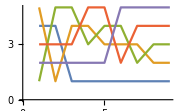

```mathematica
ListLinePlot[%]
```

He aquí el resultado para ordenar una lista aleatoria de longitud 20:

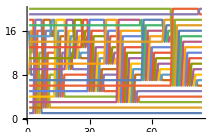

```mathematica
ListLinePlot[Transpose[FixedPointList[(#/.{x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomSample[Range[20]]]]]
```

Vocabulario

patt/;cond |   | un patrón que coincide sujeto a una condición
_ _ _ |   | un patrón para cualquier secuencia de cero o más elementos
(“triple guion-bajo”)
patt .. |   | un patrón para una o más repeticiones de patt
Longest[patt] |   | un patrón que elige la secuencia más larga con la que coincide
FixedPointList[f,x] |   | sigue anidando f hasta que el resultado ya no cambie

"12 Exercises Available" | "Get Started »"

Encuentre la lista de los dígitos de aquellos cuadrados de los números hasta 100 que contengan dígitos sucesivos repetidos. »

| Expected output: |  
  | {{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}} |

En los primeros 100 números romanos, encuentre los que contengan L, I y X, en ese orden. »

| Expected output: |  
  | {"XLIX","LIX","LXIX","LXXIX","LXXXIX"} |

Defina una función que pruebe si una lista de enteros es igual a la misma, pero en orden inverso. »

En el artículo de Wikipedia sobre “alliteration”, encuentre la lista de las parejas de palabras sucesivas cuyas letras iniciales sean idénticas. »

| Sample expected output: |  
  | {{"same","sounds"},{"or","of"},{"stressed","syllables"},{"alphabet","and"},{"to","the"},{"to","the"},{"lazy","languid"},{"Peter","Piper"},{"Piper","Picked"},{"Pickled","Peppers"},{"wind","will"},{"agreement","akin"},{"to","the"},{"stressed","syllable"},{"as","alliterating"},{"of","outside"},{"same","sound"},{"of","outside"},{"to","the"},{"brown","blazers"},{"fundamentally","for"},{"colour","co-ordination"},{"in","its"},{"silken","sad"},{"furrow","followed"},{"followed","free"},{"stood","still"},{"Alphabetical","Africa"},{"chapter","consists"},{"at","all"},{"written","with"},{"Brent","Bernard"},{"who","watch"},{"watch","with"},{"with","wild"},{"wild","wonder"},{"wide","window"},{"beautiful","birds"},{"birds","begin"},{"bountiful","birdseed"},{"Grey","Geese"},{"grey","geese"},{"Betty","Botter"},{"Betty","Botter"},{"butter","but"},{"she","said"},{"butter's","bitter"},{"it","in"},{"make","my"},{"batter","bitter"},{"bitter","but"},{"better","butter"},{"make","my"},{"bitter","batter"},{"batter","better"},{"Peter","Piper"},{"Piper","Peter"},{"Peter","Piper"},{"pickled","peppers"},{"Peter","Piper"},{"pickled","peppers"},{"pickled","peppers"},{"Peter","Piper"},{"Irish","It"},{"important","ingredient"},{"Æthelwulf","Æthelbald"},{"Æthelbald","Æthelberht"},{"direct","descendants"},{"Tancred","Torhtred"},{"poetry","poets"},{"can","call"},{"splendid","silent"},{"silent","sun"},{"Walt","Whitman"},{"Splendid","Silent"},{"Silent","Sun"},{"wondered","what"},{"his","horse"},{"also","add"},{"to","the"},{"harsh","hard"},{"they","than"},{"slippered","sleep"},{"lean","lithe"},{"fleet","flown"},{"E.","E."},{"an","artistic"},{"that","the"},{"out","of"},{"as","an"},{"an","artistic"},{"constraint","can"},{"it","is"},{"emotional","effect"},{"as","a"},{"and","attention"},{"as","a"},{"persuasive","public"},{"any","attitude"},{"as","a"},{"adds","a"},{"an","audience’s"},{"audience’s","attention"},{"noticeable","nature"},{"evokes","emotion"},{"an","audience"},{"them","to"},{"to","the"},{"can","create"},{"is","in"},{"twenty-one","times"},{"times","throughout"},{"as","an"},{"which","we"},{"our","only"},{"of","our"},{"our","own"},{"but","by"},{"today","that"},{"that","the"},{"truths","that"},{"is","inextricably"},{"to","the"},{"itself","is"},{"testimony","to"},{"to","the"},{"have","had"},{"because","brave"},{"freedom's","front"},{"Ronald","Reagan"},{"Vietnam","Veterans"},{"new","nation"},{"to","the"},{"modern","music"},{"cartoon","characters"},{"If","I"},{"Anadiplosis","Assonance"},{"Tautogram","Tongue"},{"alliterations","and"}} |

Use Grid para mostrar el proceso de ordenamiento dado en esta sección para {4,5,1,3,2}, donde los pasos sucesivos se presenten en forma vertical. »

| Expected output: |  
  | 4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5 |

Use ArrayPlot para mostrar el proceso de ordenamiento visto en esta sección para una lista de longitud 50, donde los pasos sucesivos aparezcan en forma horizontal. »

| Sample expected output: |  
  | -Graphics- |

Empezando con 1.0, aplicar repetidamente la función del “método de Newton ”,  (#+2/# )/2& hasta que el resultado ya no cambie. »

| Expected output: |  
  | {1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421} |

Implemente el algoritmo de Euclides para el máximo común divisor, donde {a,b} se sustituya repetidamente por {b,Mod[a,b]} hasta que b sea 0, y aplicar el algoritmo a 12345, 54321. »

| Expected output: |  
  | {{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}} |

Defina combinadores usando las reglas s[x_][y_][z_]→x[z][y[z]],k[x_][y_]→x, y luego generar una lista empezando con s[s][k][s[s[s]][s]][s] y aplicando dichas reglas hasta que no haya cambios. »

| Expected output: |  
  | {s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]} |

Elimine todos los ceros al final de la lista de dígitos de 100!. »

| Expected output: |  
  | {9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4} |

Comenzando con {1,0}, elimine repetidamente los primeros 2 elementos y pegue {0,1} si el primer elemento es 1, y {1,0,0} si es 0, en 200 pasos; obtenga la lista de las longitudes de las secuencias así producidas (sistema de etiquetas). »

| Expected output: |  
  | {2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125} |

Comenzando con {0,0} y por 200 pasos, elimine repetidamente los primeros 2 elementos y pegue {2,1} si el primer elemento es 0; {0} si el primer elemento es 1, y {0,2,1,2} si es 2; cree una gráfica con los puntos unidos de las longitudes de las secuencias producidas (sistema de etiquetas). »

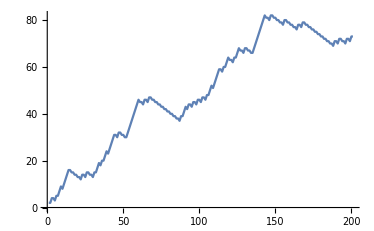
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Qué otras funciones que trabajen con patrones hay en Wolfram Language?

Except[patt] coincide con cualquier cosa, excepto patt. PatternSequence[patt] coincide con una secuencia de argumentos en una función. OrderlessPatternSequence[patt] coincide con dichos argumentos sin importar el orden. f[x_:v] define a v como valor por defecto, así que en f[ ], x se toma como v.

¿Cómo pueden verse todas las formas en que un patrón podría coincidir con una expresión dada?

Use ReplaceList. Replace obtiene la primera coincidencia; ReplaceList obtiene la lista de todas ellas.

¿Qué hace FixedPointList cuando no hay un punto fijo?

En algún momento se detendrá. Existe, además, una opción para fijar qué tan lejos debe llegar. FixedPointList[f,x,n] se detiene después de un máximo de n pasos.

Notas técnicas

En el caso de un patrón repetitivo patt.., recuerde que debe dejarse un espacio, por ejemplo, cuando se tiene 0 .. para evitar la confusión con números decimales.

Las funciones pueden tener atributos que afecten el funcionamiento de la coincidencia de patrones. Por ejemplo, Plus tiene los atributos Flat y Orderless. Flat significa que b+c puede extraerse de a+b+c+d. Orderless significa que los elementos pueden reordenarse, de tal modo que a+c puede sacarse. (Flat es como la propiedad matemática de la asociatividad; Orderless es como la conmutatividad).

El algoritmo que se ha mostrado para efectuar un ordenamiento se conoce usualmente como ordenamiento de burbuja. Para una lista de longitud n, tomará por lo general alrededor de n^2 pasos. La función nativa de Wolfram Language, Sort, es mucho más rápida y toma apenas un poco más de n pasos.

Para explorar más

Guía para patrones en Wolfram Language »